```mathematica
data1=Import["/home/tony/Workspace/local/benchmark/inflight_1.csv"];
data2=Import["/home/tony/Workspace/local/benchmark/inflight_2.csv"];
data3=Import["/home/tony/Workspace/local/benchmark/inflight_3.csv"];
data4=Import["/home/tony/Workspace/local/benchmark/inflight_4.csv"];
data5=Import["/home/tony/Workspace/local/benchmark/inflight_5.csv"];
data6=Import["/home/tony/Workspace/local/benchmark/inflight_6.csv"];
data7=Import["/home/tony/Workspace/local/benchmark/inflight_7.csv"];
data8=Import["/home/tony/Workspace/local/benchmark/inflight_8.csv"];
```

```mathematica
data1Time=Transpose[data1][[1]];
data2Time=Transpose[data2][[1]];
data3Time=Transpose[data3][[1]];
data4Time=Transpose[data4][[1]];
data5Time=Transpose[data5][[1]];
data6Time=Transpose[data6][[1]];
data7Time=Transpose[data7][[1]];
data8Time=Transpose[data8][[1]];
```

```mathematica
dataTime=Transpose[{data1Time,data2Time,data3Time,data4Time,data5Time,data6Time,data7Time,data8Time}];
dataSpeed=(2^20*8)/(dataTime/1000000);
meanTime=Table[Mean[dataSpeed[[i]]],{i,1,40}];
SDTime=Table[StandardDeviation[dataSpeed[[i]]],{i,1,40}];
mean=ListLinePlot[meanTime];
SDMin=ListLinePlot[meanTime-SDTime,PlotStyle->Dashed];
SDMax=ListLinePlot[meanTime+SDTime,PlotStyle->Dashed];
meanDot=ListPlot[meanTime];
max=ListLinePlot[Table[Max[meanTime],{i,0,100}]];
```

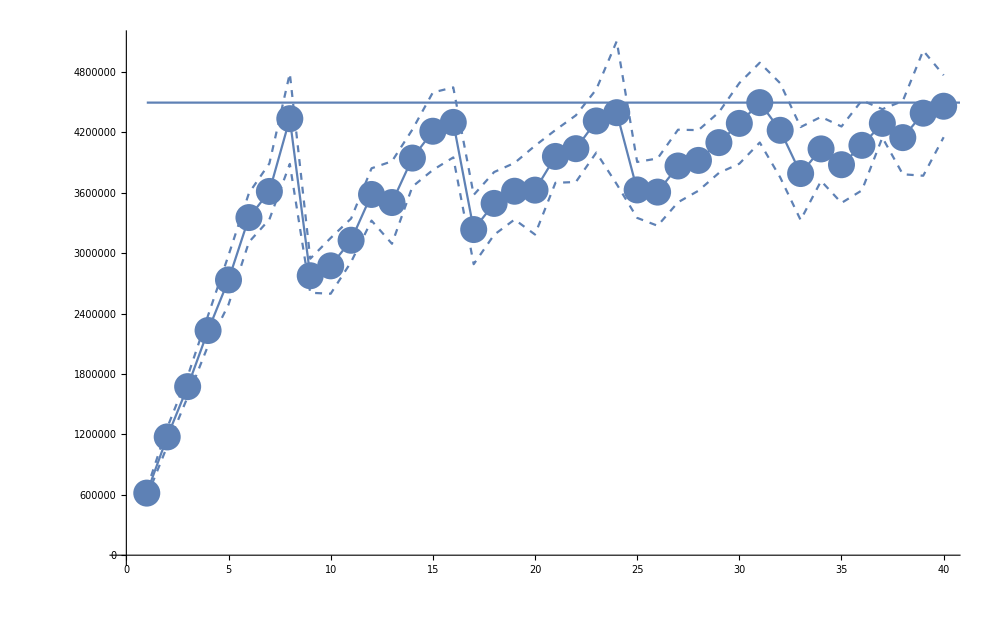

```mathematica
Show[SDMax,SDMin,mean,meanDot,max,ImageSize->1000]
```